l1

l1

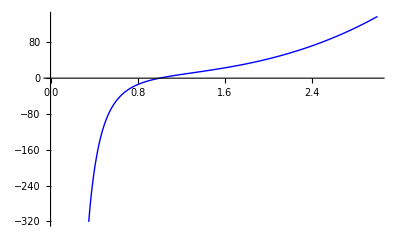

Listplot[{(-10+10 l1^2+5 (-1+l1^6))/l1^3}]

1

1

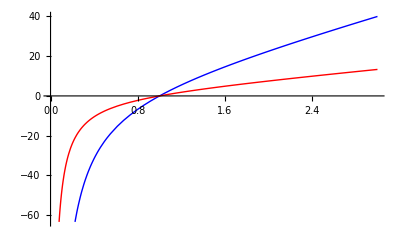

Listplot[{(-10+10 l1^2+5 (-1+l1^2))/l1,(5 (-1+l1^2))/l1}]

l3

√(-1/l1^2-(√(1+3 l1^2))/l1^2)

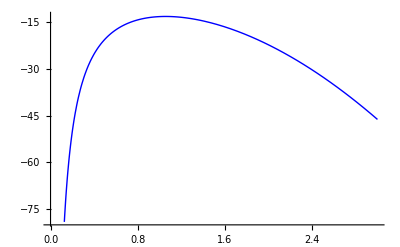

Listplot[{(-10+10 l1^2+5 (-1+(-1/l1-(√(1+3 l1^2))/l1)^2))/(-1/l1-(√(1+3 l1^2))/l1)}]

l3

l3

-Graphics-

Listplot[{(-10+10 l1^2+5 (-1+l1^2 l3^4))/(l1 l3^2)}]

```mathematica
Clear["Global`*"]; 
(* CIARLET-Energie *)

(*LAMÉsche Parameter*)
l=10;m=10;

(*Deformationsgradiententensor*)
F={{l1,0,0},{0,l2,0},{0,0,l3}};

(*Konstitutivgesetz*)
T[F_]:=1/Det[F]*(m*F.Transpose[F]+(l/2*(Det[F]*Det[F]-1)-m)*IdentityMatrix[3])
(*T[F_]:=1/Det[F]*(l*Tr[1/2*(Transpose[F].F-IdentityMatrix[3])]*F.Transpose[F]+m (F.Transpose[F].F.Transpose[F]-F.Transpose[F]))*)

(* Fall 1: Kompression bzw. Expansion*)
l2=l1
l3=l1
Plot[T[F][[1,1]],{l1,0,3},PlotStyle->{Blue}]
Listplot[{T[F][[1,1]]}]
Clear[l2,l3]

(*Fall 2: Zugversuch mit festgehaltener e_2- und e_3-Richtung*)
l2=1
l3=1
Plot[{T[F][[1,1]],T[F][[2,2]]},{l1,0,3},PlotStyle->{Blue, Red}]
Listplot[{T[F][[1,1]],T[F][[2,2]]}]
Clear[l2,l3]

(*Fall 3: Zugversuch*)
l2=l3
l3=l3/.Solve[T[F][[3,3]]==0,l3][[2]]  (*Normierung*)
Plot[{T[F][[1,1]]},{l1,0,3},PlotStyle->{Blue}]
Listplot[{T[F][[1,1]]}]
Clear[l2,l3]

(*3D-Plot fuer Fall 3 da ja eigentlich von l1 und l2 abhaengig*)
l2=l3
l3=l3

DensityPlot[{T[F][[1,1]]},{l1,0,5},{l3,0,5},PlotRange->{-600,600},ColorFunction->(Blend[{Red,White,Blue},#1]&),Mesh->Full,MeshStyle->White,PlotLegends->Automatic]
Listplot[{T[F][[1,1]]}]
```